```mathematica
x:={0.0, 0.5, 1.0}
y:=Exp[x]
```

```mathematica
x[[1]]
y[[1]]
```

0.

1.

```mathematica
l0[t_]:=((t-x[[2]])*(t-x[[3]]))/(((x[[1]]-x[[2]])*(x[[1]]-x[[3]])))
l1[t_]:=((t-x[[1]])*(t-x[[3]]))/(((x[[2]]-x[[1]])*(x[[2]]-x[[3]])))
l2[t_]:=((t-x[[1]])*(t-x[[2]]))/(((x[[3]]-x[[1]])*(x[[3]]-x[[2]])))
```

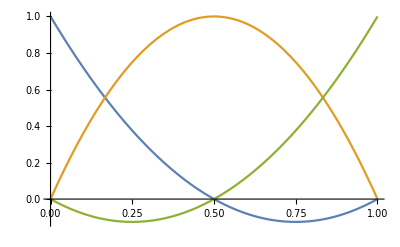

```mathematica
Plot[{l0[t], l1[t],l2[t]},{t,x[[1]], x[[3]]}]
```

```mathematica
P[t_]:=y[[1]]*l0[t]+y[[2]]*l1[t]+y[[3]]*l2[t]
Expand[P[t]]
```

1.+0.876603 t+0.841679 t^2

```mathematica
a:=Plot[P[t],{t,x[[1]],x[[3]]}]
b:=ListPlot[Table[{x[[j]],y[[j]]},{j,1,3}]]
```

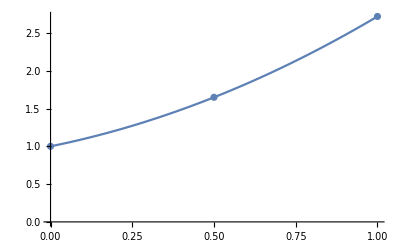

```mathematica
Show[b,a]
```

```mathematica
Table[{x[[j]],y[[j]]},{j,1,3}]
```

{{0.,1.},{0.5,1.64872},{1.,2.71828}}